Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Scenario B: mid water influx, water_in=500

Define parameters:

```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;dw=0.4;
alpha=0.4;
beta=300;
p=1;
kh=0.1;
kw=0.01;
n=0.1;
a=0.5;
```

Define water recharge rates:

```mathematica
win=500;
ws=alpha*(win-beta);

wt= win-ws;
```

Define system without fire effects

```mathematica
dhdt[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
```

```mathematica
dwdt[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W
p3=Plot3D[dhdt[H,W],{H,0,400},{W,0,400},PlotStyle->Blue];
p4=Plot3D[dwdt[H,W],{H,0,400},{W,0,400}];
Show[p3,p4]
```

-Graphics3D-

Find Fixed points

```mathematica
Simplify[Solve[dhdt[H,W]==0,H]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→386.667-0.6 W}}

```mathematica
Simplify[Solve[H==386.6666666666667-0.6*W,W]]
```

{{W→644.444-1.66667 H}}

```mathematica
p1=Plot[644.4444444444445-1.666666666667*H,{H,0,300}];
```

```mathematica
Simplify[Solve[dwdt[H,W]==0,W]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{W→245.833-0.833333 H-0.833333 √(106225.-350. H+H^2)},{W→0.833333 (295.-1. H+√(106225.-350. H+H^2))}}

```mathematica
p2=Plot[0.8333333333333334* (295- H+√(106225-350* H+H^2)),{H,0,300},PlotStyle->Red];
p5=Plot[245.83333333333334-0.8333333333333334*H-0.8333333333333334*√(106225-350*H+H^2),{H,0,300},PlotStyle->Red];
```

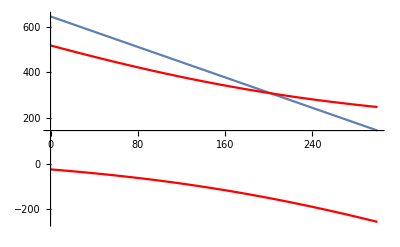

```mathematica
Show[p1,p2,p5,PlotRange->All]
```

```mathematica
fp=Simplify[Solve[dwdt[H,W]==0 && dhdt[H,W]==0,{H,W}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.,W→-25.7681},{H→202.051,W→307.692},{H→0.,W→517.435}}

```mathematica
fp1=Part[fp,1]
```

{H→0.,W→-25.7681}

```mathematica
fp2=Part[fp,2]
```

{H→202.051,W→307.692}

```mathematica
fp3=Part[fp,3]
```

{H→0.,W→517.435}

Partial Derivatives evaluated at first fixed point: unstable

```mathematica
j11=D[dhdt[H,W],H]/.fp1
```

5.60768

```mathematica
j12=D[dhdt[H,W],W]/.fp1
```

0.

```mathematica
j21=D[dwdt[H,W],H]/.fp1
```

0.779485

```mathematica
j22=D[dhdt[H,W],W]/.fp1
```

0.

```mathematica
J={{j11,j12},{j21,j22}}
Eigenvalues[J]
Eigenvectors[J]
```

{{5.60768,0.},{0.779485,0.}}

{5.60768,0.}

{{0.990477,0.137679},{0.,1.}}

Partial Derivatives evaluated at second fixed point: stable

```mathematica
j11=D[dhdt[H,W],H]/.fp2
```

-0.38967

```mathematica
j12=D[dhdt[H,W],W]/.fp2
```

-0.233802

```mathematica
j21=D[dwdt[H,W],H]/.fp2
```

-0.178022

```mathematica
j22=D[dhdt[H,W],W]/.fp2
```

-0.233802

```mathematica
J={{j11,j12},{j21,j22}}
Eigenvalues[J]
Eigenvectors[J]
```

{{-0.38967,-0.233802},{-0.178022,-0.233802}}

{-0.53013,-0.0933429}

{{-0.857205,-0.514975},{0.619415,-0.785064}}

Partial Derivatives evaluated at third fixed point: unstable

```mathematica
j11=D[dhdt[H,W],H]/.fp3;
j12=D[dhdt[H,W],W]/.fp3;
j21=D[dwdt[H,W],H]/.fp3;
j22=D[dhdt[H,W],W]/.fp3;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{0.175652,0.}